826

1174

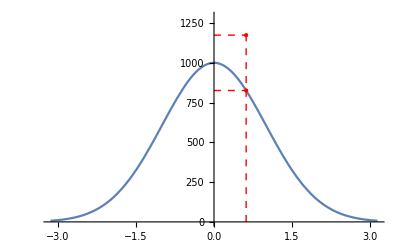

```mathematica
μ = 0; 
σ = 1; 
ε = 0.618; 
x = 1000; 

distribution = NormalDistribution[μ, σ]; 
theta = x/PDF[distribution, 0]; 

deviance = (PDF[distribution, 0] - PDF[distribution, ε])*theta; 

lower = Round[x - deviance]
upper = Round[x + deviance]

Plot[PDF[distribution, x]*theta, {x, -Pi, Pi}, 
  Epilog -> {
{Red, PointSize[Large], Point[{{ε, lower}, {ε, upper}}]},
{Red, Dashed, Line[{
{{0, lower}, {ε, lower}},
{{0, upper}, {ε, upper}}, 
{{ε, 0}, {ε, upper}}
}]
}}, 
  PlotRange -> {{-Pi, Pi}, {0, upper*1.1}}]
```